# Automatic Differentation

## Brian Beckman March 2024

```mathematica
If[Or[PacletFind["DualNumbers"]==={},
PacletFind["DualNumbers"][[1]]["Version"]=!="1.3.0"],
PacletInstall[$HomeDirectory<>"/Documents/GitHub/DualNumbers/Paclet archives/DualNumbers-1.3.0.paclet"]]
```

```mathematica
<<DualNumbers`
```

```mathematica
Normal @ Series[f[a + b ε], {ε, 0, 4}] /. Power[ε, _?(GreaterEqualThan[2])] -> 0
```

f[a]+b ε f'[a]

### Fixed Points of Cos

```mathematica
f[a_]:=Module[{x=1.,y,i=0},While[Not[(y=Cos[a x])==x],x=y;
i++];
{x,Log10[1+i]}];
```

### Value and Log10 of Iteration Count

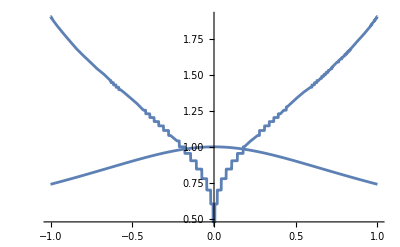

```mathematica
Plot[f[a],{a,-1.0,1.0}]
```

### Derivative

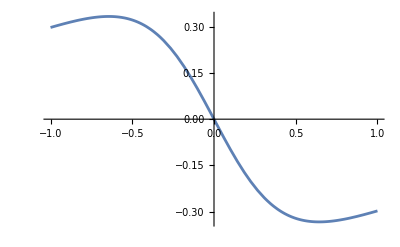

```mathematica
Plot[NonStandard[f[Dual[a,1]][[1]]],{a,-1.0,1.0}]
```

```mathematica
Cos[Dual[a,1]]
```

Cos[a]-Sin[a] ε

### Multidimensional Functions

```mathematica
g[x_,y_]:=Sin[x y]/(x^2+y^2);
Plot3D[g[x,y],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
d=(g[Dual[0.5,b1],Dual[2.,b2]]//Simplify)
```

0.197993+(0.207673 b1-0.122782 b2) ε

```mathematica
NonStandard[d]
```

0.207673 b1-0.122782 b2

```mathematica
grad=D[g[x,y],{{x,y}}]/.{x->0.5,y->2.}
```

{0.207673,-0.122782}

### Dual Arrays

```mathematica
dvec=Dual[#,1.]&/@RandomReal[1,5]
```

{0.0908729+1. ε,0.795747+1. ε,0.347846+1. ε,0.292586+1. ε,0.465444+1. ε}

### Poking Around

```mathematica
Names["DualNumbers`*"]//TableForm
```

AddDualHandling
Dual
DualApply
DualArrayQ
DualExpand
DualFactor
DualFindMaximum
DualFindMinimum
DualFindRoot
DualFreeArrayQ
DualLinearSolveFunction
DualQ
DualScalarQ
DualSimplify
DualTuples
DualTuplesReduce
FindDualSolution
NonStandard
OpenExampleNotebook
PackDualArray
Standard
StandardAll
StandardNonStandard
StandardQ
ToDual
UnpackDualArray
UnpackedDualArrayQ
ε

```mathematica
DualNumbers`OpenExampleNotebook[]
```

```mathematica
ClearAll[f,g,h,w,w0,w1,w2,w3];
w0=x;w1=h[w0];w2=g[w1];w3=f[w2];y=w3;
w0=Dual[x,1];
w1=Dual[h[w0],1];
w2=Dual[g[w1],1];
w3=Dual[f[w2],1];
y=w3;
```